# Modelos Matemáticos y Algoritmos - Ejercicio 1

## Jesús Bueno Urbano - 20078941X

## Apartado 2

A continuación comprobamos con varios ejemplos que si se cumple la condición r < de.b2 la solución permanece estable para cualquier valor de τ.

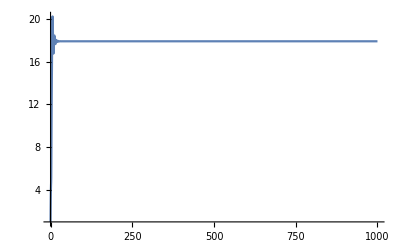

```mathematica
r=6;
d=1;
τ=2;
k=10;
sol:=NDSolve[{x'[t]==r*x[t-τ]Exp[-x[t-τ]/k]-d*x[t],x[0]==1},x[t],{t,0,1000}]
gr=Plot[Evaluate[x[t]/.sol],{t,0,1000},PlotRange->All]
```

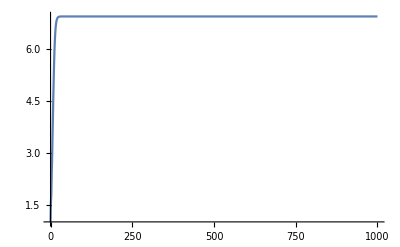

```mathematica
r=2;
d=1;
τ=2;
k=10;
sol:=NDSolve[{x'[t]==r*x[t-τ]Exp[-x[t-τ]/k]-d*x[t],x[0]==1},x[t],{t,0,1000}]
gr=Plot[Evaluate[x[t]/.sol],{t,0,1000},PlotRange->All]
```

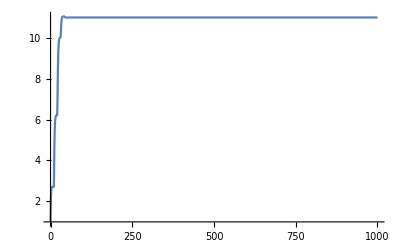

```mathematica
r=3;
d=1;
τ=10;
k=10;
sol:=NDSolve[{x'[t]==r*x[t-τ]Exp[-x[t-τ]/k]-d*x[t],x[0]==1},x[t],{t,0,1000}]
gr=Plot[Evaluate[x[t]/.sol],{t,0,1000},PlotRange->All]
```

## Apartado 3

Tras haber calculado los valores críticos de ν y de τ. Pasamos a ver su efecto alrededor del valor crítico de τ.

```mathematica
r=8;
d=1;
k=10;
```

```mathematica
ν=Sqrt[(1-Log[r/d])^2-1];
τ=ArcCos[1/(1-Log[r/d])]/ν - 1;
sol1:=NDSolve[{x'[t]==r*x[t-τ]Exp[-x[t-τ]/k]-d*x[t],x[0]==1},x[t],{t,0,1000}];
gr1=Plot[Evaluate[x[t]/.sol],{t,0,1000},PlotRange->All];
```

```mathematica
ν=Sqrt[(1-Log[r/d])^2-1];
τ=ArcCos[1/(1-Log[r/d])]/ν - 0.1;
sol2:=NDSolve[{x'[t]==r*x[t-τ]Exp[-x[t-τ]/k]-d*x[t],x[0]==1},x[t],{t,0,1000}];
gr2=Plot[Evaluate[x[t]/.sol],{t,0,1000},PlotRange->All];
```

```mathematica
ν=Sqrt[(1-Log[r/d])^2-1];
τ=ArcCos[1/(1-Log[r/d])]/ν + 0.1;
sol3:=NDSolve[{x'[t]==r*x[t-τ]Exp[-x[t-τ]/k]-d*x[t],x[0]==1},x[t],{t,0,1000}];
gr3=Plot[Evaluate[x[t]/.sol],{t,0,1000},PlotRange->All];
```

```mathematica
ν=Sqrt[(1-Log[r/d])^2-1];
τ=ArcCos[1/(1-Log[r/d])]/ν + 1;
sol4:=NDSolve[{x'[t]==r*x[t-τ]Exp[-x[t-τ]/k]-d*x[t],x[0]==1},x[t],{t,0,1000}];
gr4=Plot[Evaluate[x[t]/.sol],{t,0,1000},PlotRange->All];
```

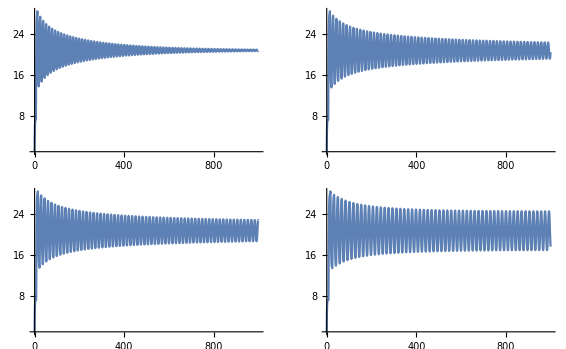

```mathematica
GraphicsGrid[{{gr1,gr2},{gr3,gr4}}]
```

Como podemos observar para valores menores que el crítico, la solución se acaba estabilizando pero, en cambio, para valores un poco superiores vemos como no ocurre.

## Apartado 4

En este apartado llamaremos a r y d, con r0 y d0 respectivamente para evitar que tomen los valores que ya hemos usado anteriormente.

```mathematica
ν0=Sqrt[(1-Log[r0/d0])^2-1];
τ0=ArcCos[1/(1-Log[r0/d0])]/ν0 ;
μ0=0;
```

```mathematica
equation1=(μ0+μ1*ϵ)+d0*((Log[r0/d0]-1)*Exp[-(μ0+μ1*ϵ)*(τ0 + ϵ)]*Cos[(ν0+ν1 *ϵ)(τ0+ϵ)]+1);
equation2=(ν0+ν1*ϵ)+d0*((Log[r0/d0]-1)*Exp[-(μ0+μ1*ϵ)*(τ0 + ϵ)]*Sin[(ν0+ν1 *ϵ)(τ0+ϵ)]);
```

```mathematica
equation1des=Normal[Series[equation1,{ϵ,0,1}]];
equation2des=Normal[Series[equation2,{ϵ,0,1}]];
```

```mathematica
equation10=FullSimplify[Coefficient[equation1des,ϵ,0],Assumptions->d0>0&&r0>d0 E^2];
equation20=FullSimplify[Coefficient[equation2des,ϵ,0],Assumptions->d0>0&&r0>d0 E^2];
```

```mathematica
equation11=Coefficient[equation1des,ϵ,1];
equation21=Coefficient[equation2des,ϵ,1];
```

```mathematica
Coeficientes=FullSimplify[Solve[{equation11 == 0, equation21 == 0}, {μ1, ν1}], Assumptions -> d0 > 0 && r0 > d0 E^2];
```

```mathematica
μ1= (d0 (1+Log[d0]-Log[r0]) (2+Log[d0]-Log[r0])^2 Log[r0/d0]^2)/(Abs[1+Log[d0]-Log[r0]] (d0^2 ArcSec[1+Log[d0]-Log[r0]]^2 (1+Log[d0]-Log[r0])^2+Log[d0/r0] (-2-Log[d0]+Log[r0])));
```

```mathematica
ν1=(d0 (-2-Log[d0]+Log[r0]) Log[r0/d0] (-Log[d0/r0]^2+d0 ArcSec[1+Log[d0]-Log[r0]] (d0 ArcSec[1+Log[d0]-Log[r0]] (1+Log[d0]-Log[r0])^2-(Log[d0/r0] (2+Log[d0]-Log[r0]))^(3/2))+2 Log[r0/d0]))/((-d0 ArcSec[1+Log[d0]-Log[r0]]+√(Log[d0/r0] (2+Log[d0]-Log[r0]))) (-Log[d0/r0]^2+d0^2 ArcSec[1+Log[d0]-Log[r0]]^2 (1+Log[d0]-Log[r0])^2+2 Log[r0/d0]));
```

```mathematica
Periodo=2*Pi/(ν0+ϵ*ν1);
```

Ahora que hemos calculado el período teórico, pasamos a las estimaciones numéricas.

```mathematica
d=1;
r=8;
ν=Sqrt[(1-Log[r/d])^2-1];
τ=ArcCos[1/(1-Log[r/d])]/ν ;
k=10;
```

```mathematica
ν0=Sqrt[(1-Log[r/d])^2-1];
τ0=ArcCos[1/(1-Log[r/d])]/ν0 ;
μ0=0;
μ1= (d (1+Log[d]-Log[r]) (2+Log[d]-Log[r])^2 Log[r/d]^2)/(Abs[1+Log[d]-Log[r]] (d^2 ArcSec[1+Log[d]-Log[r]]^2 (1+Log[d]-Log[r])^2+Log[d/r] (-2-Log[d]+Log[r])));
ν1=(d (-2-Log[d]+Log[r]) Log[r/d] (-Log[d/r]^2+d ArcSec[1+Log[d]-Log[r]] (d ArcSec[1+Log[d]-Log[r]] (1+Log[d]-Log[r])^2-(Log[d/r] (2+Log[d]-Log[r]))^(3/2))+2 Log[r/d]))/((-d ArcSec[1+Log[d]-Log[r]]+√(Log[d/r] (2+Log[d]-Log[r]))) (-Log[d/r]^2+d^2 ArcSec[1+Log[d]-Log[r]]^2 (1+Log[d]-Log[r])^2+2 Log[r/d]));
```

```mathematica
Periodo=2*Pi/(ν0+ϵ*ν1);
N[Periodo,5]
N[τ0,5]
```

6.2832/(0.40644-0.068824 ϵ)

6.7797

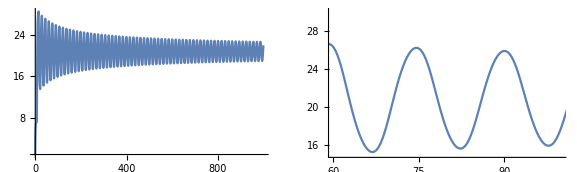

```mathematica
sol:=NDSolve[{x'[t]==r*x[t-τ]Exp[-x[t-τ]/k]-d*x[t],x[0]==1},x[t],{t,0,1000}];
gr=Plot[Evaluate[x[t]/.sol],{t,0,1000},PlotRange->All];
grs=Show[gr,PlotRange->{{60,100},{15,30}}];
GraphicsGrid[{{gr,grs}}]
```

```mathematica
FindRoot[Evaluate[x[t]/.sol]==k*Log[r/d],{t,0,10}]
```

{t→8.54792}

```mathematica
8.54792*2
Periodo
```

17.0958

15.46

En este caso podemos observar como el período numérico no se aleja mucho del teórico.

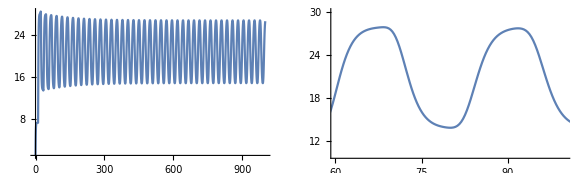

```mathematica
sol:=NDSolve[{x'[t]==r*x[t-11]Exp[-x[t-11]/k]-d*x[t],x[0]==1},x[t],{t,0,1000}];
gr=Plot[Evaluate[x[t]/.sol],{t,0,1000},PlotRange->All];
grs=Show[gr,PlotRange->{{60,100},{10,30}}];
GraphicsGrid[{{gr,grs}}]
```

```mathematica
FindRoot[Evaluate[x[t]/.sol]==k*Log[r/d],{t,0,10}]
```

{t→779.202}

```mathematica
779.202*2
Periodo
```

1558.4

15.46

En este caso, con τ mayor que el valor crítico, vemos como el período no se parece.